# Parameterized Event Records Data Transformations

## Introduction

In this document (notebook) we describe transformations of events records data in order to make that data more amenable for the application of Machine Learning (ML) algorithms.

Consider the following problem formulation (done with the next five bullet points.)

From data representing a (most likely very) diverse set of events we want to derive contingency matrices corresponding to each of the variables in that data.

The events are observations of the values of a certain set of variables for a certain set of entities. Not all entities have events for all variables.

The observation times do not form a regular time grid.

Each contingency matrix has rows corresponding to the entities in the data and has columns corresponding to time.

The software component providing the functionality should allow parametrization and repeated execution. (As in ML classifier training and testing scenarios.)

The phrase “event records data” is used instead of “time series” in order to emphasize that (i) some variables have categorical values, and (ii) the data can be given in some general database form, like transactions long-form.

The required transformations of the event records in the problem formulation above are done through the monad ERTMon, [AAp3]. (The name ERTMon comes from “Event Records Transformations Monad”.)

The monad code generation and utilization is explained in [AA1] and implemented with [AAp1].

It is assumed that the event records data is put in a form that makes it (relatively) easy to extract time series for the set of entity-variable pairs present in that data.

In brief ERTMon performs the following sequence of transformations.

The event records of each entity-variable pair are shifted to adhere to a specified start or end point,

The event records for each entity-variable pair are aggregated and normalized with specified functions over a specified regular grid,

Entity vs. time interval contingency matrices are made for each combination of variable and aggregation function.

The transformations are specified with a “computation specification” dataset.

Here is an example of an ERTMon pipeline over event records:

ERTMonUnit[] ⟹ | initialize the monad pipeline
  ERTMonSetEventRecords[eventRecords] ⟹ | ingest event records
  ERTMonSetEntityAttributes[entityAttributes] ⟹ | ingest event attributes
  ERTMonSetComputationSpecification[compSpec] ⟹ | ingest computation specification
  ERTMonGroupEntityVariableRecords ⟹ | group records per {EntityID, Variable}
  ERTMonEntityVariableGroupsToTimeSeries["MaxTime"] ⟹ | align the event records and create time series
  ERTMonAggregateTimeSeries | aggregate the time series
(according to the computation specification)

The rest of the document describes in detail:

the structure, format, and interpretation of the event records data and computations specifications,

the transformations of time series aligning, aggregation, and normalization,

the software pattern design -- a monad -- that allows sequential specifications of desired transformations.

Concrete examples are given using weather data. See [AAp9].

## Paclet load

Load the paclet and supporting ones

```mathematica
Needs["AntonAntonov`MonadicEventRecordsTransformations`"];
Needs["AntonAntonov`DataReshapers`"];
Needs["AntonAntonov`OutlierIdentifiers`"];
Needs["AntonAntonov`SSparseMatrix`"];
```

## Data load

The data we use is weather data from meteorological stations close to certain major cities. We retrieve the data with the function WeatherEventRecords from the package [AAp9].

```mathematica
?WeatherEventRecords
```

```mathematica
citiesSpec={{"Miami","USA"},{"Jacksonville","USA"},{"Chicago","USA"},{"London","UK"},{"Melbourne","Australia"},{"Sydney","Australia"}};
dateRange={{2024,10,1},{2025,10,1}};
wProps={"Temperature","MaxTemperature","Pressure","Humidity","WindSpeed"};
res=WeatherEventRecords[citiesSpec,dateRange,wProps,0];
```

Here we assign the obtained datasets to variables we use below:

```mathematica
eventRecords=res["eventRecords"];
entityAttributes=res["entityAttributes"];
```

Here are the summaries of the datasets eventRecords and entityAttributes:

```mathematica
RecordsSummary[eventRecords]
```

{1 EntityID
Chicago_USA | 1621
Jacksonville_USA | 1616
Miami_USA | 1616
Melbourne_Australia | 1580
London_UK | 1264
Sydney_Australia | 1264,2 LocationID
Chicago | 1621
Jacksonville | 1616
Miami | 1616
Melbourne | 1580
London | 1264
Sydney | 1264,3 ObservationTime
Min | 3936729600
1st Qu | 3943900800
Mean | 3.95111×10^9
Median | 3951331200
3rd Qu | 3958243200
Max | 3965241600,4 Variable
Temperature | 1923
Humidity | 1922
MaxTemperature | 1913
WindSpeed | 1607
Pressure | 1596,5 Value
Min | -17.67
1st Qu | 5.61
Median | 17.22
3rd Qu | 27.22
Mean | 192.135
Max | 1039.2}

```mathematica
RecordsSummary[entityAttributes]
```

{1 EntityID
Chicago_USA | 2
Jacksonville_USA | 2
London_UK | 2
Melbourne_Australia | 2
Miami_USA | 2
Sydney_Australia | 2,2 Attribute
City | 6
Country | 6,3 Value
USA | 3
Australia | 2
Chicago | 1
Jacksonville | 1
London | 1
Melbourne | 1
(Other) | 3}

## Design considerations

### Workflow

The steps of the main event records transformations workflow addressed in this document follow.

Ingest event records and entity attributes given in the Star schema style.

Ingest a computation specification.

Specified are aggregation time intervals, aggregation functions, normalization types and functions.

Group event records based on unique entity ID and variable pairs.

Additional filtering can be applied using the entity attributes.

For each variable find descriptive statistics properties.

This is to facilitate normalization procedures.

Optionally, for each variable find outlier boundaries.

Align each group of records to start or finish at some specified point.

For each variable we want to impose a regular time grid.

From each group of records produce a time series.

For each time series do prescribed aggregation and normalization.

The variable that corresponds to each group of records has at least one (possibly several) computation specifications.

Make a contingency matrix for each time series obtained in the previous step.

The contingency matrices have entity ID’s as rows, and time intervals enumerating values of time intervals.

The following flow-chart corresponds to the list of steps above.

```mathematica
img=Import["~/Documents/Conceptual diagrams/Event records transformations workflows/ERTMon-workflows.jpg"];
ImageResize[img,1200]
AutoCollapse[]
```

-Graphics-

A corresponding monadic pipeline is given in the section “Larger example pipeline”.

### Feature engineering perspective

The workflow above describes a way to do feature engineering over a collection of event records data. For a given entity ID and a variable we derive several different time series.

Couple of examples follow.

One possible derived feature (times series) is for each entity-variable pair we make time series of the hourly mean value in each of the eight most recent hours for that entity. The mean values are normalized by the average values of the records corresponding to that entity-variable pair.

Another possible derived feature (time series) is for each entity-variable pair to make a time series with the number of outliers in the each half-hour interval, considering the most recent 20 half-hour intervals. The outliers are found by using outlier boundaries derived by analyzing all values of the corresponding variable, across all entities.

From the examples above -- and some others -- we conclude that for each feature we want to be able to specify:

maximum history length (say from the most recent observation),

aggregation interval length,

aggregation function (to be applied in each interval),

normalization function (per entity, per cohort of entities, per variable),

conversion of categorical values into numerical ones.

### Repeated execution

We want to be able to do repeated executions of the specified workflow steps.

Consider the following scenario. After the event records data is converted to a entity-vs-feature contingency matrix, we use that matrix to train and test a classifier. We want to find the combination of features that gives the best classifier results. For that reason we want to be able to easily and systematically change the computation specifications (interval size, aggregation and normalization functions, etc.) With different computation specifications we obtain different entity-vs-feature contingency matrices, that would have different performance with different classifiers.

Using the classifier training and testing scenario we see that there is another repeated execution perspective: after the feature engineering is done over the training data, we want to be able to execute exactly the same steps over the test data. Note that with the training data we find certain global or cohort normalization values and outlier boundaries that have to be used over the test data. (Not derived from the test data.)

The following diagram further describes the repeated execution workflow.

```mathematica
img=Import["~/Documents/Conceptual diagrams/Event records transformations workflows/ERTMon-repeated-execution-workflow.jpg"];
ImageResize[img,1200]
AutoCollapse[]
```

-Graphics-

Further discussion of making and using ML classification workflows through the monad software design pattern can be found in [AA2].

## Event records data design

The data is structured to follow the style of Star schema. We have event records dataset (table) and entity attributes dataset (table).

The structure datasets (tables) proposed satisfy a wide range of modeling data requirements. (Medical and financial modeling included.)

### Entity event data

The entity event data has the columns “EntityID”, “LocationID”, “ObservationTime”, “Variable”, “Value”.

```mathematica
RandomSample[eventRecords,6]
```

Most events can be described through “Entity event data”. The entities can be anything that produces a set of event data: financial transactions, vital sign monitors, wind speed sensors, chemical concentrations sensors.

The locations can be anything that gives the events certain "spatial" attributes: medical units in hospitals, sensors geo-locations, tiers of financial transactions.

### Entity attributes data

The entity attributes dataset (table) has attributes (immutable properties) of the entities. (Like, gender and race for people, longitude and latitude for wind speed sensors.)

```mathematica
entityAttributes⟦1;;6⟧
```

### Example

For example, here we take all weather stations in USA:

```mathematica
ws=Normal[entityAttributes[Select[#Attribute=="Country"&&#Value=="USA"&],"EntityID"]]
```

{Miami_USA,Jacksonville_USA,Chicago_USA}

Here we take all temperature event records for those weather stations:

```mathematica
srecs=eventRecords[Select[#Variable=="Temperature"&&MemberQ[ws,#EntityID]&]];
```

And here plot the corresponding time series obtained by grouping the records by station (entity ID’s) and taking the columns “ObservationTime” and ”Value”:

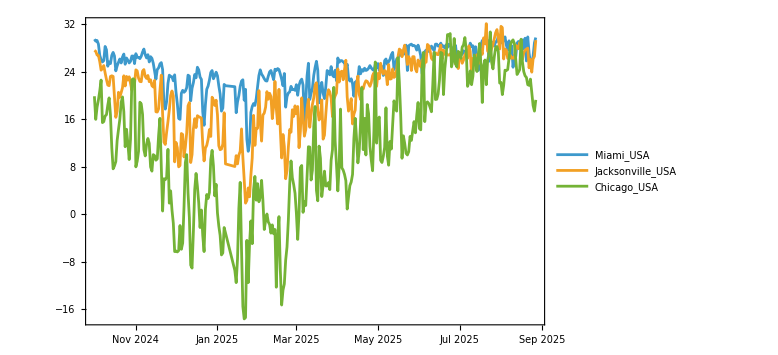

```mathematica
grecs=Normal@GroupBy[srecs,#EntityID&][All,All,{"ObservationTime","Value"}];
DateListPlot[grecs,ImageSize->Large,PlotTheme->"Detailed"]
```

## Monad elements

This section goes through the steps of the general ERTMon workflow.For didactic purposes each sub-section changes the pipeline assigned to the variable p. Of course all functions can be chained into one big pipeline as shown in the section “Larger example pipeline”.

### Monad unit

The monad is initialized with ERTMonUnit.

```mathematica
ERTMonUnit[]
```

ERTMon[…]

### Ingesting event records and entity attributes

The event records dataset (table) and entity attributes dataset (table) are set with corresponding setter functions. Alternatively, they can be read from files in a specified directory.

```mathematica
p=
ERTMonUnit[]⟹
ERTMonSetEventRecords[eventRecords]⟹
ERTMonSetEntityAttributes[entityAttributes]⟹
ERTMonEchoDataSummary;
```

Data summary:  <|eventRecords→{1 EntityID
Chicago_USA | 1621
Jacksonville_USA | 1616
Miami_USA | 1616
Melbourne_Australia | 1580
London_UK | 1264
Sydney_Australia | 1264,2 LocationID
Chicago | 1621
Jacksonville | 1616
Miami | 1616
Melbourne | 1580
London | 1264
Sydney | 1264,3 ObservationTime
Min | 3936729600
1st Qu | 3943900800
Mean | 3.95111×10^9
Median | 3951331200
3rd Qu | 3958243200
Max | 3965241600,4 Variable
Temperature | 1923
Humidity | 1922
MaxTemperature | 1913
WindSpeed | 1607
Pressure | 1596,5 Value
Min | -17.67
1st Qu | 5.61
Median | 17.22
3rd Qu | 27.22
Mean | 192.135
Max | 1039.2},entityAttributes→{1 EntityID
Chicago_USA | 2
Jacksonville_USA | 2
London_UK | 2
Melbourne_Australia | 2
Miami_USA | 2
Sydney_Australia | 2,2 Attribute
City | 6
Country | 6,3 Value
USA | 3
Australia | 2
Chicago | 1
Jacksonville | 1
London | 1
Melbourne | 1
(Other) | 3}|>

### Computation specification

Using the package [AAp3] we can create computation specification dataset. Below is given an example of constructing a fairly complicated computation specification.

The package EmptyComputationSpecificationRow can be used to construct the rows of the specification.

```mathematica
EmptyComputationSpecificationRow[]
```

<|Variable→Missing[],Explanation→,MaxHistoryLength→3600,AggregationIntervalLength→60,AggregationFunction→Mean,NormalizationScope→Entity,NormalizationFunction→None|>

```mathematica
compSpecRows=Join[EmptyComputationSpecificationRow[],<|"Variable"->#,"MaxHistoryLength"->60*24*3600,"AggregationIntervalLength"->2*24*3600,"AggregationFunction"->"Mean","NormalizationScope"->"Entity","NormalizationFunction"->"Mean"|>]&/@Union[Normal[eventRecords[All,"Variable"]]];
compSpecRows=
Join[
compSpecRows,Join[EmptyComputationSpecificationRow[],<|"Variable"->#,"MaxHistoryLength"->60*24*3600,"AggregationIntervalLength"->2*24*3600,"AggregationFunction"->"Range","NormalizationScope"->"Country","NormalizationFunction"->"Mean"|>]&/@Union[Normal[eventRecords[All,"Variable"]]],
Join[EmptyComputationSpecificationRow[],<|"Variable"->#,"MaxHistoryLength"->60*24*3600,"AggregationIntervalLength"->2*24*3600,"AggregationFunction"->"OutliersCount","NormalizationScope"->"Variable"|>]&/@Union[Normal[eventRecords[All,"Variable"]]]
];
```

The constructed rows are assembled into a dataset (with Dataset). The function ProcessComputationSpecification is used to convert a user-made specification dataset into a form used by ERTMon.

```mathematica
wCompSpec=ProcessComputationSpecification[Dataset[compSpecRows]][SortBy[#Variable&]]
```

The computation specification is set to the monad with the function ERTMonSetComputationSpecification.

Alternatively, a computation specification can be created and filled-in as a CSV file and read into the monad. (Not described here.)

### Grouping event records by entity-variable pairs

With the function ERTMonGroupEntityVariableRecords we group the event records by the found unique entity-variable pairs. Note that in the pipeline below we set the computation specification first.

```mathematica
p=
p⟹
ERTMonSetComputationSpecification[wCompSpec]⟹
ERTMonGroupEntityVariableRecords;
```

### Descriptive statistics (per variable)

After the data is ingested into the monad and the event records are grouped per entity-variable pairs we can find certain descriptive statistics for the data. This is done with the general function ERTMonComputeVariableStatistic and the specialized function  ERTMonFindVariableOutlierBoundaries.

```mathematica
p⟹ERTMonComputeVariableStatistic[RecordsSummary]⟹ERTMonEchoValue;
```

value:  <|Humidity→{1 column 1
Min | 0.209
1st Qu | 0.611
Mean | 0.701364
Median | 0.717
3rd Qu | 0.798
Max | 1.},MaxTemperature→{1 column 1
Min | -17.22
1st Qu | 16
Mean | 20.9305
Median | 22.72
3rd Qu | 27.22
Max | 40.22},Pressure→{1 column 1
Min | 990.8
1st Qu | 1014.1
Mean | 1017.56
Median | 1017.7
3rd Qu | 1021.1
Max | 1039.2},Temperature→{1 column 1
Min | -17.67
1st Qu | 12.0725
Mean | 17.4833
Median | 18.72
3rd Qu | 23.7075
Max | 32.06},WindSpeed→{1 column 1
Min | 0
1st Qu | 9.82
Median | 13.52
Mean | 14.118
3rd Qu | 17.78
Max | 38.89}|>

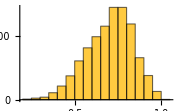
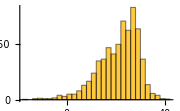
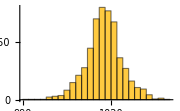
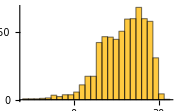
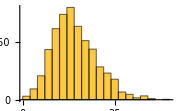
value:  <|Humidity→-Graphics-,MaxTemperature→-Graphics-,Pressure→-Graphics-,Temperature→-Graphics-,WindSpeed→-Graphics-|>

```mathematica
p⟹ERTMonComputeVariableStatistic⟹ERTMonEchoValue;
```

```mathematica
p⟹ERTMonComputeVariableStatistic[TakeLargest[#,3]&]⟹ERTMonEchoValue;
```

value:  <|Humidity→{1.,0.996,0.996},MaxTemperature→{40.22,40.22,39},Pressure→{1039.2,1037.6,1036.8},Temperature→{32.06,31.83,31.61},WindSpeed→{38.89,34.63,34.08}|>

### Finding the variables outlier boundaries

The finding of outliers counts and fractions can be specified in the computation specification. Because of this there is a specialized function for outlier finding ERTMonFindVariableOutlierBoundaries. That function makes the association of the found variable outlier boundaries (i) to be the pipeline value and (ii) to be the value of context key “variableOutlierBoundaries”. The outlier boundaries are found using the functions of the package [AAp6].

If no argument is specified ERTMonFindVariableOutlierBoundaries uses the Hampel identifier (HampelIdentifierParameters).

```mathematica
p⟹ERTMonFindVariableOutlierBoundaries⟹ERTMonEchoValue;
```

value:  <|Humidity→{0.579118,0.854882},MaxTemperature→{14.9808,30.4592},Pressure→{1012.51,1022.89},Temperature→{10.3285,27.1115},WindSpeed→{7.75269,19.2873}|>

```mathematica
Keys[p⟹ERTMonFindVariableOutlierBoundaries⟹ERTMonTakeContext]
```

{eventRecords,entityAttributes,computationSpecification,entityVariableRecordGroups,variableOutlierBoundaries}

In the rest of document we use the outlier boundaries found with the more conservative identifier SPLUSQuartileIdentifierParameters.

```mathematica
p=
p⟹
ERTMonFindVariableOutlierBoundaries[SPLUSQuartileIdentifierParameters]⟹ERTMonEchoValue;
```

value:  <|Humidity→{0.3305,1.0785},MaxTemperature→{-0.83,44.05},Pressure→{1003.6,1031.6},Temperature→{-5.43,41.21},WindSpeed→{-2.12,29.72}|>

### Conversion of event records to time series

The grouped event records are converted into time series with the function ERTMonEntityVariableGroupsToTimeSeries. The time series are aligned to a time point specification given as an argument. The argument can be: a date object, “MinTime”, “MaxTime”, or “None”. (“MaxTime” is the default.)

```mathematica
p⟹
ERTMonEntityVariableGroupsToTimeSeries["MinTime"]⟹
ERTMonEchoFunctionContext[#timeSeries⟦{1,3,5}⟧&];
```

<|{Miami_USA,Temperature}→TimeSeries[…],{Miami_USA,Pressure}→TimeSeries[…],{Miami_USA,WindSpeed}→TimeSeries[…]|>

Compare the last output with the output of the following command.

```mathematica
p=
p⟹
ERTMonEntityVariableGroupsToTimeSeries["MaxTime"]⟹
ERTMonEchoFunctionContext[#timeSeries⟦{1,3,5}⟧&];
```

<|{Miami_USA,Temperature}→TimeSeries[…],{Miami_USA,Pressure}→TimeSeries[…],{Miami_USA,WindSpeed}→TimeSeries[…]|>

### Time series restriction and aggregation.

The main goal of ERTMon is to convert a diverse, general collection of event records into a collection of aligned time series over specified regular time grids.

The regular time grids are specified with the columns “MaxHistoryLength” and “AggregationIntervalLength” of the computation specification. The time series of the variables in the computation specification are restricted to the corresponding maximum history lengths and are aggregated using the corresponding aggregation lengths and functions.

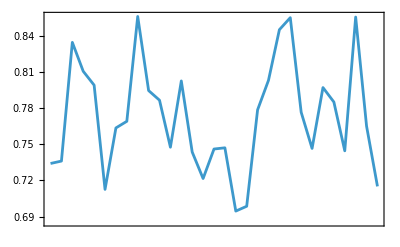
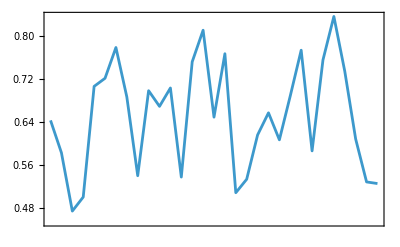
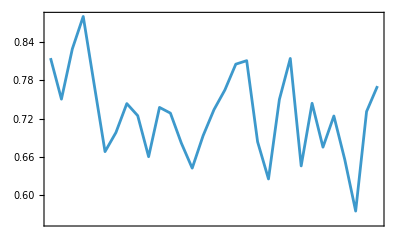
<|{Miami_USA,Humidity.Mean}→-Graphics-,{Chicago_USA,Humidity.Mean}→-Graphics-,{Melbourne_Australia,Humidity.Mean}→-Graphics-|>

```mathematica
p=
p⟹
ERTMonAggregateTimeSeries⟹
ERTMonEchoFunctionContext[DateListPlot/@#timeSeries⟦{1,3,5}⟧&];
```

### Application of time series functions

At this point we can apply time series modifying functions. An often used such function is moving average.

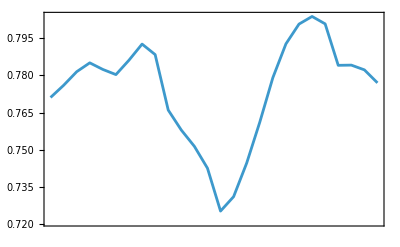
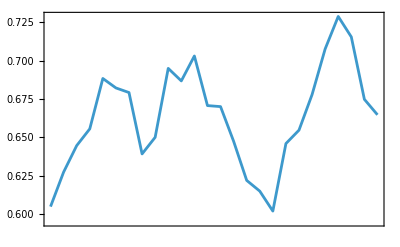
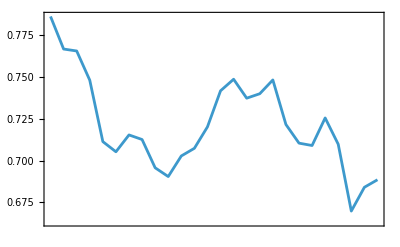
<|{Miami_USA,Humidity.Mean}→-Graphics-,{Chicago_USA,Humidity.Mean}→-Graphics-,{Melbourne_Australia,Humidity.Mean}→-Graphics-|>

```mathematica
p⟹
ERTMonApplyTimeSeriesFunction[MovingAverage[#,6]&]⟹
ERTMonEchoFunctionValue[DateListPlot/@#⟦{1,3,5}⟧&];
```

Note that the result is given as a pipeline value, the value of the context key ”timeSeries” is not changed.

(In the future, the computation specification and its handling might be extended to handle moving average or other time series function specifications.)

### Normalization

With “normalization” we mean that the values of a given time series values are divided (normalized) with a descriptive statistic derived from a specified set of values. The specified set of values is given with the parameter “NormalizationScope” in computation specification.

At the normalization stage each time series is associated with an entity ID and variable.

Normalization is done at three different scopes: “entity”, “attribute”, and “variable”.

Given a time series T(i,var) corresponding to entity ID i and a variable var we define the normalization values for the different scopes in the following ways.

Normalization with scope “entity” means that the descriptive statistic is derived from the values of T(i,var) only.

Normalization with scope attribute means that

from the entity attributes dataset we find attribute value that corresponds to i,

next we find all entity ID's that are associated with the same attribute value,

next we find value of normalization descriptive statistic using the time series that correspond to the variable var and the entity ID’s found in the previous step.

Normalization with scope ”variable” means that the descriptive statistic is derived from the values of all time series corresponding to var.

Note that the scope “entity” is the most granular, and the scope “variable” is the coarsest.

The following command demonstrates the normalization effect -- compare the y-axes scales of the time series corresponding to the same entity-variable pair.

<|{Miami_USA,Humidity.Mean}→-Graphics-,{Chicago_USA,Humidity.Mean}→-Graphics-,{Melbourne_Australia,Humidity.Mean}→-Graphics-|>

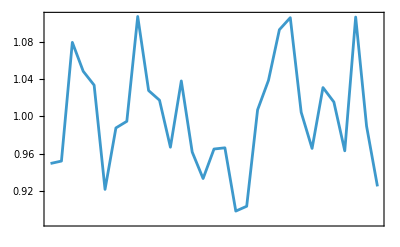
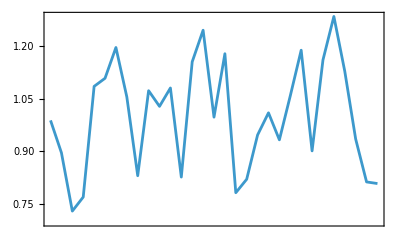
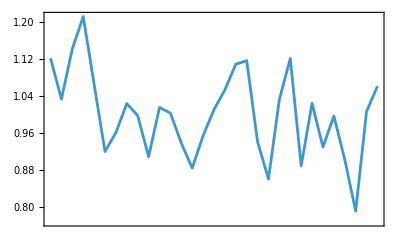
<|{Miami_USA,Humidity.Mean}→-Graphics-,{Chicago_USA,Humidity.Mean}→-Graphics-,{Melbourne_Australia,Humidity.Mean}→-Graphics-|>

```mathematica
p=
p⟹
ERTMonEchoFunctionContext[DateListPlot/@#timeSeries⟦{1,3,5}⟧&]⟹
ERTMonNormalize⟹
ERTMonEchoFunctionContext[DateListPlot/@#timeSeries⟦{1,3,5}⟧&];
```

Here are the normalization values that should be used when normalizing “unseen data.”

```mathematica
p⟹ERTMonTakeNormalizationValues
```

<|{Humidity.Range,Country,USA}→0.0656344,{Humidity.Range,Country,UK}→0.0674839,{Humidity.Range,Country,Australia}→0.0926935,{MaxTemperature.Range,Country,USA}→2.29452,{MaxTemperature.Range,Country,UK}→72/31,{MaxTemperature.Range,Country,Australia}→1.76065,{Pressure.Range,Country,USA}→1.36022,{Pressure.Range,Country,Australia}→4.42742,{Temperature.Range,Country,USA}→1.50505,{Temperature.Range,Country,UK}→1.48645,{Temperature.Range,Country,Australia}→1.48403,{WindSpeed.Range,Country,USA}→3.58247,{WindSpeed.Range,Country,UK}→3.64387,{WindSpeed.Range,Country,Australia}→4.53355|>

### Making contingency matrices

One of the main goals of ERTMon is to produce contingency matrices corresponding to the event records data.

The contingency matrices are created and stored as SSparseMatrix objects, [AAp7].

```mathematica
p=
p⟹ERTMonMakeContingencyMatrices;
```

We can obtain an association of the contingency matrices for each variable-and-aggregation-function pair, or obtain the overall contingency matrix.

```mathematica
p⟹ERTMonTakeContingencyMatrices
Dimensions/@%
```

<|Humidity.Mean→SparseArray[…],Humidity.OutliersCount→SparseArray[…],Humidity.Range→SparseArray[…],MaxTemperature.Mean→SparseArray[…],MaxTemperature.OutliersCount→SparseArray[…],MaxTemperature.Range→SparseArray[…],Pressure.Mean→SparseArray[…],Pressure.OutliersCount→SparseArray[…],Pressure.Range→SparseArray[…],Temperature.Mean→SparseArray[…],Temperature.OutliersCount→SparseArray[…],Temperature.Range→SparseArray[…],WindSpeed.Mean→SparseArray[…],WindSpeed.OutliersCount→SparseArray[…],WindSpeed.Range→SparseArray[…]|>

<|Humidity.Mean→{6,31},Humidity.OutliersCount→{6,31},Humidity.Range→{6,31},MaxTemperature.Mean→{6,31},MaxTemperature.OutliersCount→{6,31},MaxTemperature.Range→{6,31},Pressure.Mean→{6,31},Pressure.OutliersCount→{6,31},Pressure.Range→{6,31},Temperature.Mean→{6,31},Temperature.OutliersCount→{6,31},Temperature.Range→{6,31},WindSpeed.Mean→{6,31},WindSpeed.OutliersCount→{6,31},WindSpeed.Range→{6,31}|>

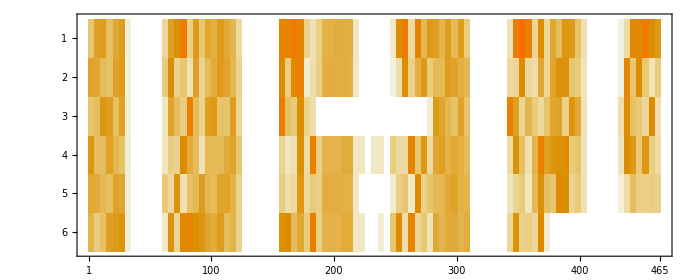

```mathematica
smat=p⟹ERTMonTakeContingencyMatrix;
MatrixPlot[smat,ImageSize->700]
```

```mathematica
RowNames[smat]
```

{Chicago_USA,Jacksonville_USA,London_UK,Melbourne_Australia,Miami_USA,Sydney_Australia}

## References

### Paclets

[AAp1] Anton Antonov, DataReshapers, (2023), Wolfram Language Paclet Repository.

[AAp2] Anton Antonov, MonadMakers, (2023), Wolfram Language Paclet Repository.

[AAp3] Anton Antonov, OutlierIdentifiers, (2023), Wolfram Language Paclet Repository.

[AAp4] Anton Antonov, SSparseMatrix, (2023), Wolfram Language Paclet Repository.

### Documents

[AA1] Anton Antonov, Monad code generation and extension, (2017), MathematicaForPrediction at WordPress.

[AA2] Anton Antonov, A monad for classification workflows, (2018), MathematicaForPrediction at WordPress.

Related Guides

Monadic Event Records Transformations

Related Tech Notes

## Metadata

### Categorization

Tech Note

AntonAntonov/MonadicEventRecordsTransformations

AntonAntonov`MonadicEventRecordsTransformations`

AntonAntonov/MonadicEventRecordsTransformations/tutorial/ParameterizedEventRecordsDataTransformations

### Keywords